# Data Science and Machine Learning II

## Author: Mathieu Bélanger Assignment 1: Green Domestic Product

In this assignment, you will calculate and explore the Green Domestic Product, an indicator developed by E4S that extends the scope of the GDP to integrate the depletion of natural, social, and human capital. In its current version, GrDP considers the impacts of the emissions of three groups of pollutants: greenhouse gases, air pollutants, heavy metals. These impacts include climate change, health issues, decrease in crops’ yields and biomass production, buildings degradation, and damages to ecosystems due to eutrophication. Read the new E4S white paper if you wish to learn more! You can also explore the results on the GrDP online dashboard. You will reproduce these results in this assignment. 

Once you are done you have to submit your notebook here: https://moodle.epfl.ch/mod/assign/view.php?id=1213652 
There is no quiz, so your grade will depend only on your notebook.
If there is need for further clarifications on the questions, after the assignment is released, we will update this file, so make sure you check the git repository for updates.
	Good luck!

## Discover the dataset

Import as a dataset the CSV file: "GrDP_Data.csv".
You can directly Import from the GitHub link: https://raw.githubusercontent.com/michalis0/MGT-529/main/Assignment/Assignment_1/GrDP_Data.csv?token=GHSAT0AAAAAABYYLB5JXSIP2RWK3C5KAP3MYZISHIQ

```mathematica
data = Import["C:\\Users\\mbela\\ecole\\MGT-529\\Assignment\\Assignment_1\\GrDP_Data.csv", "Dataset", "HeaderLines" -> 1];
```

Question 1: 
Preview the dataset. Display a random sample of the dataset [1 point]

```mathematica
RandomSample[data,10]
```

Question 2: 
How many observations (rows) does the dataset contain? [1 point]

```mathematica
(Dimensions @ data)[[1]]
```

600

Question 3: 
Extract the name of the column to understand what information is displayed in the dataset [1 point]

```mathematica
data[Keys][1]   // Normal
```

{Country,Year,GDP [million Euro],Population,Emissions_GHG [thousand tonnes CO2eq],Emissions_NOx [tonne],Emissions_PM2.5 [tonne],Emissions_PM10 [tonne],Emissions_SOx [tonne],Emissions_NMVOC [tonne],Emissions_NH3 [tonne],Emissions_Pb [tonne],Emissions_Cd [tonne],Emissions_Hg [tonne],Emissions_As [tonne],Emissions_Ni [tonne],Emissions_Cr [tonne],Cost_GHG [Euro per tonnes CO2eq],Cost_NOx [Euro per tonne],Cost_PM2.5 [Euro per tonne],Cost_PM10 [Euro per tonne],Cost_SOx [Euro per tonne],Cost_NMVOC [Euro per tonne],Cost_NH3 [Euro per tonne],Cost_Pb [Euro per kg],Cost_Cd [Euro per kg],Cost_Hg [Euro per kg],Cost_As [Euro per kg],Cost_Ni [Euro per kg],Cost_Cr [Euro per kg]}

Question 4: 
What is the scope of countries? Years? [1 point]

```mathematica
countries = DeleteDuplicates @ Normal @ data[All, "Country"];
countryEntities = Interpreter["Country"][#] & /@ countries
```

{Belgium,Bulgaria,Czech Republic,Denmark,Germany,Estonia,Ireland,Greece,Spain,France,Croatia,Italy,Cyprus,Latvia,Lithuania,Luxembourg,Hungary,Malta,Netherlands,Austria,Poland,Portugal,Romania,Slovenia,Slovakia,Finland,Sweden,Norway,Switzerland,United Kingdom}

```mathematica
GeoListPlot[ countryEntities]
```

-Graphics-

```mathematica
DeleteDuplicates @ data[All, "Year"]
```

## Exploratory Data Analysis

Question 5: 
Plot the evolution of the emissions of NOx for the country of your choice [1 point]

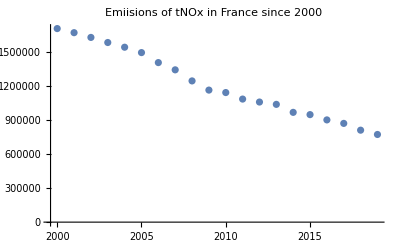

```mathematica
ListPlot[data[Select[#Country == "France"&],{"Year", "Emissions_NOx [tonne]"}], PlotLabel->"Emiisions of tNOx in France since 2000"]
```

Question 6: 
Create a scatter plot of the natural logarithm of PM10 and GHG emissions (considering all countries and years). [1 point]

```mathematica
emissionLogs = data[All, { "Emissions_GHG [thousand tonnes CO2eq]" -> Log, "Emissions_PM10 [tonne]" -> Log}];
```

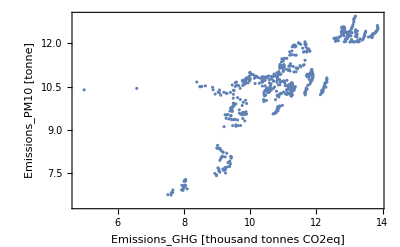

```mathematica
ListPlot[emissionLogs[All, {"Emissions_GHG [thousand tonnes CO2eq]" , "Emissions_PM10 [tonne]" }], Frame -> True, FrameLabel-> {"Emissions_GHG [thousand tonnes CO2eq]", "Emissions_PM10 [tonne]"}]
```

Question 7:   
Compute the correlation matrix between GDP and the emissions of pollutants. Display the correlation matrix in a dataset where the rows and columns are labelled [1 point]

```mathematica
correlationColumns = {"GDP [million Euro]","Emissions_GHG [thousand tonnes CO2eq]","Emissions_NOx [tonne]","Emissions_PM2.5 [tonne]","Emissions_PM10 [tonne]","Emissions_SOx [tonne]","Emissions_NMVOC [tonne]","Emissions_NH3 [tonne]","Emissions_Pb [tonne]","Emissions_Cd [tonne]","Emissions_Hg [tonne]","Emissions_As [tonne]","Emissions_Ni [tonne]","Emissions_Cr [tonne]"};
```

```mathematica
Correlation[Normal @ data[All, "GDP [million Euro]"],  Normal @ data[All, "Emissions_NOx [tonne]"]]
```

0.852084

```mathematica
correlationMatrix = Correlation[Normal[ Values /@ data[All, correlationColumns]]];
```

```mathematica
corrMat=Dataset[AssociationThread[correlationColumns->(AssociationThread[correlationColumns->#]&/@correlationMatrix)]]
```

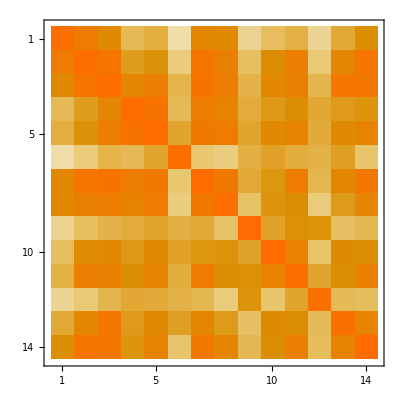

```mathematica
Correlation[Normal @ Map[Values,data[All, correlationColumns]]] // MatrixPlot
```

## Calculating GrDP

GrDP is defined as the GDP minus the external costs of pollutants.
The external costs of a given pollutant are calculated by multiplying the emissions by the marginal damage cost (unit cost).

```mathematica
countries = Normal @ data[All, "Country"];
years = Normal @ data[All, "Year"];
```

Question 8: 
Compute the total external costs in million euros for all countries and years (be careful of units...) [1 point]

We have two differently formatted costs columns [Euro per Tonne] [Euro per kg]  and the units for GHG which are in thousands of tonne

```mathematica
pollutantsKg = {"Pb", "Cd", "Hg", "As", "Ni", "Cr"};
pollutantsT = {"NOx", "PM2.5", "PM10", "SOx", "NMVOC", "NH3"};
```

```mathematica
costPollutantsGHG = (Normal @ data[All, "Emissions_GHG [thousand tonnes CO2eq]"]) * (Normal @ data[All,"Cost_GHG [Euro per tonnes CO2eq]"]) * 1000;
costsPollutantsT = Map[Normal @ data[All, "Emissions_" <> # <> " [tonne]"] * Normal @ data[All, "Cost_" <> # <> " [Euro per tonne]"]&, pollutantsT];
costsPollutantsKg = Map[(Normal @ data[All, "Emissions_" <> # <> " [tonne]"] * Normal @ data[All, "Cost_" <> # <> " [Euro per kg]"])* 1000 &, pollutantsKg];
```

```mathematica
totalCosts = (Total[costsPollutantsT] + Total[costsPollutantsKg] + costPollutantsGHG) / 1000000;
```

```mathematica
costDataset = Transpose @ Dataset @ AssociationThread[{"Country", "Year", "Total external cost [million Euro]"} -> {countries, years , totalCosts} ]
Export["C:\\Users\\mbela\\ecole\\MGT-529\\Assignment\\Assignment_1\\ext_costs.csv",costDataset]
```

C:\Users\mbela\ecole\MGT-529\Assignment\Assignment_1\ext_costs.csv

Question 9 : 
Compute the share of external costs with respect to GDP in percentage [1 point]

```mathematica
ExtCostsToGDP = Transpose @ Dataset @ AssociationThread[{"Country", "Year", "Share of external costs to GDP"} -> {countries,years, totalCosts / (Normal @ data[All, "GDP [million Euro]"])} ]
```

Question 10: 
Compute the GrDP per capita in euros for all countries and years [1 point]

```mathematica
GrDP = (Normal @ data[All, "GDP [million Euro]"]) - totalCosts;
GrDPCapita = (GrDP / Normal @ data[All, "Population"]) * 1000000;
```

```mathematica
GrDPCapitaDataset = Transpose @ Dataset @ AssociationThread[{"Country", "Year", "GrDP per capita [Euro]"} -> {countries, years, GrDPCapita } ]
```

Question 11: 
What are the share of external costs and GrDP per capita in Italy in 2005?  [1 point]

```mathematica
ExtCostsToGDP[Select[{#Country, #Year} == {"Italy", 2005}& ]]
GrDPCapitaDataset[Select[{#Country, #Year} == {"Italy", 2005}&]]
```

## Visualizing the results

Question 12: 
Create a bar chart of the share of external costs for all countries in 2019, where the countries are sorted from lowest to highest share of external cost  [1 point]

```mathematica
orderedCountries = ReverseSortBy[ExtCostsToGDP[Select[#Year == 2019&] // Normal], #[[3]]&][All, {"Country", "Share of external costs to GDP"}];
```

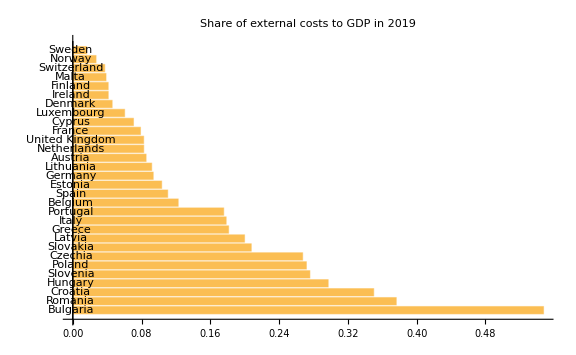

```mathematica
BarChart[orderedCountries[All, "Share of external costs to GDP"],BarOrigin-> Left, ImageSize-> Large,PlotLabel->"Share of external costs to GDP in 2019", ChartLabels->Normal @ orderedCountries[All, "Country"]]
```

Question 13: 
Create a map of the GrDP per capita in 2019  [1 point]

```mathematica
GrDP2019 = GrDPCapitaDataset[Select[#Year == 2019&]];
```

```mathematica
countryEntities = Interpreter["Country"][#] & /@ Normal @ GrDP2019[All, "Country"];
```

```mathematica
GeoRegionValuePlot[AssociationThread[countryEntities ->Normal @ GrDP2019[All, "GrDP per capita [Euro]"]], PlotLabel->"GrDP per capita [Euro] in 2019"]
```

-Graphics-

Question 14: 
Upgrade your previous map, adding an interactive feature allowing to select the year   [1 point]

```mathematica
Manipulate[GeoRegionValuePlot[
AssociationThread[countryEntities -> Normal @ GrDPCapitaDataset[Select[#Year == Year&],"GrDP per capita [Euro]"]],
GeoLabels->Tooltip[countryEntities]],
{Year, 2000, 2019, 1},
 ContinuousAction->False,
 FrameLabel->"GrDP per capita in Europe (2000-2019)"
]
```

GeoRegionValuePlot::ldata: <|countryEntities→GrDPCapitaDataset[Select[#Year==FE`Year$$161&],GrDP per capita [Euro]]|> is not a valid dataset or list of datasets.

GeoRegionValuePlot::ldata: <|countryEntities→GrDPCapitaDataset[Select[#Year==FE`Year$$661&],GrDP per capita [Euro]]|> is not a valid dataset or list of datasets.

GeoRegionValuePlot::ldata: <|countryEntities→GrDPCapitaDataset[Select[#Year==FE`Year$$1800&],GrDP per capita [Euro]]|> is not a valid dataset or list of datasets.

GeoRegionValuePlot::ldata: <|Belgium→GrDPCapitaDataset[Select[#Year==FE`Year$$1800&],GrDP per capita [Euro]],Bulgaria→GrDPCapitaDataset[Select[#Year==FE`Year$$1800&],GrDP per capita [Euro]],Czech Republic→GrDPCapitaDataset[Select[#Year==FE`Year$$1800&],GrDP per capita [Euro]],«25»,Switzerland→GrDPCapitaDataset[Select[#Year==FE`Year$$1800&],GrDP per capita [Euro]],United Kingdom→GrDPCapitaDataset[Select[#Year==FE`Year$$1800&],GrDP per capita [Euro]]|> is not a valid dataset or list of datasets.

## Predicting GrDP...

Question 15: 
Build a linear regression model predicting GrDP per capita using the GDP, Population and all the emissions of pollutants. Split your dataset into training set and test set.  [1 point]

```mathematica
regressionColumns =  {"GDP [million Euro]","Population", "Emissions_GHG [thousand tonnes CO2eq]","Emissions_NOx [tonne]","Emissions_PM2.5 [tonne]","Emissions_PM10 [tonne]","Emissions_SOx [tonne]","Emissions_NMVOC [tonne]","Emissions_NH3 [tonne]","Emissions_Pb [tonne]","Emissions_Cd [tonne]","Emissions_Hg [tonne]","Emissions_As [tonne]","Emissions_Ni [tonne]","Emissions_Cr [tonne]", "GrDP per capita [Euro]"};
```

```mathematica
regressionData = Join[data, GrDPCapitaDataset, 2][All, regressionColumns];
{nObs, nCol} = Dimensions[regressionData];
```

```mathematica
{trainingSet, testSet} = TakeDrop[regressionData, Floor[nObs *0.8]];
```

```mathematica
pGrDP = Predict[trainingSet -> "GrDP per capita [Euro]", Method->"LinearRegression"] 
Information[pGrDP]
```

PredictorFunction[…]

Predictor information
Data type | Mixed (number: 15)
Standard deviation | 12900. ± 1600.
Method | LinearRegression
Single evaluation time | 2.34 ms/example
Batch evaluation speed | 115. examples/ms
Loss | 10.9 ± 0.12
Model memory | 362. kB
Training examples used | 480 examples
Training time | 3.01 s
 |

Question 16: 
What are the L1 and L2 regularization coefficients of your predictor?  [1 point]

```mathematica
Information[pGrDP, "L1Regularization"]
Information[pGrDP, "L2Regularization"]
```

0

1.×10^-6

Question 17: 
Assess the performance of your predictor on the test set. [1 point]

We can see, looking at the R-squared and RMSE that the predictions are pretty poor.  Our model explains only 31.5% of the variance and the root-average of the squared residuals is 17 900 Euros.

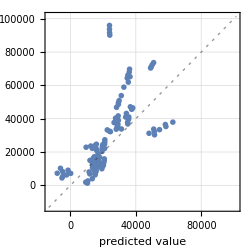
Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 120
Standard deviation | 17700. ± 2200.
Standard deviation baseline | 21700. ± 1700.
R-squared | 0.335 ± 0.2
Mean cross entropy | 11.3 ± 0.22
Single evaluation time | 11.9 ms/example
Batch evaluation speed | 1.44 examples/ms
-Graphics- |

```mathematica
measurmentsGrDP = PredictorMeasurements[pGrDP, testSet]
```

```mathematica
Show[measurmentsGrDP["SHAPPlots"], ImageSize -> Large]
```

-Graphics-

-Graphics-